# Spin Echo Data Analysis

## Module

```mathematica
(* This Program created by Jacob Embley, 2015. Modified by Scott Leland Crossen, May 2016. *)

Clear["`*"];
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarPlots`"]


list={};
string="";
outlist={};




(* FF= Find Frequency:
Calculates the ideal frequency setting for the function generator (in other words, the frequency of the laser pulses).
The entire duration of the laser/microwave pulses (including another 150 ns called "extra" simply ensure that the sequence fits comfortably)*)
(*Input: delay2= length of Subscript[T, fixed] for the particular spin echo scan *)
FF[delay2_]:=Module[{delay1,width1,width2,delay3,width3,extra,i},

(* width1 and width2 represent the π and π/2 pulses, as named in the LabVIEW scan program.  These should be changed for each set of spin echo scans *)
width1=220;
width2=420;

(* delay1 accounts for the inherent physical delay of our set-up (switches, signal travel time, etc. *)
delay1=3640;

(* delay3 accounts for the Subscript[T, fixed] value (delay2), plus a extra time for the longest scan points (when Subscript[T, varied]>Subscript[T, fixed]).  The extra time here (currently 600 ns) should be equal to the amount of time that you set for each scan on either side of the echo (in this case, the extra value is 600 because Subscript[T, fixed]=1000 ns and an example scan would go from Subscript[T, varied]=400 ns to 1600 ns)*)
delay3=delay2+600;

(* width3 is the second π/2 pulse *)
width3=width1;

(* this is the extra time that was explained above (ensures things fit comfortably)*)
extra=150;

(* i= total length of entire pulse sequence in ns *)
i=delay1+width1+delay2+width2+delay3+width3+extra;

(* now converts from ns to s *)
i=i*1*^-9;

(* Changes period in s to frequency in kHz.  It also rounds decimals down to the closest integer frequency *)
i=IntegerPart[1/i/1000];

(* Prints the best frequency for the user to select when performing echo scans *)
Print["Set frequency to ",i,"kHz"]]




(* FileImport: Imports the experiment data from the output of the LabVIEW scan program *)
(* Input: name=the file name with extension (must be in the same folder as this notebook or else list full file path.  This file name should be inputted as a string, or in other words, with quotation marks *)
FileImport[name_String]:=Module[{newName,data={},i1,i2,test=False,files=FileNames[]},

(* This Do loop checks to see if the file can be found. It assigns "test" a value of True or False *)
Do[If[name==files[[i]],test=True],{i,Length[files]}];

(* If the file was found, it will now import that data *)
If[test,

(* The method here is somewhat strange, but it works... because Mathematica fails to import these .xls files properly, you must change the file extension to .tsv (tab seperated values).  Yes...we should probably just save them that way in the first place, but habits are hard to break.  So we create a copy of the file as a .tsv, import it, then delete the .tsv copy of the file. *) 
newName=StringDrop[name,-4]<>".tsv";
CopyFile[name,newName];
data=Import[newName];
DeleteFile[newName];

(* The now imported LabVIEW files have markers in the form of "==========" to seperate the header, notes, and data.  So we start at the top of the file and scan through the code, looking for two of these markers (signifying the start of the actual data).  The value of i1 becomes the index of the first data point. *)
i1=1;
While[data[[i1,1]]≠"==========",i1=i1+1];
i1=i1+1;
While[data[[i1,1]]≠"==========",i1=i1+1];
i2=i1;

(* The marker for the end of the data is "****", so i2 becomes the index for the end of the data *)
While[data[[i2,1]]≠"****",i2=i2+1];

(* The function ouputs a two-valued: the first value indicating whether or not the file was found and the second value with the imported data. *) 
{test,Take[data,{i1+2,i2-1}]},
{test,0}]
]




(* GaussianEcho: Function to fit the imported data to a sloped gaussian function, plot the results, and add the results to "list" *)
(* Inputs:
	fileName: Name of the file which contains the data (as a string)
	DropPointsBefore: The number of data points that will be ignored at the beginning
DropPointsAfter: The number of data points that will be ignored at the end
Include: (True/False)Whether or not you want the results of this data fit to be included in the data summary plots/calculations are the end of this notebook*) 
GaussianEcho[fileName_,DropPointsBefore_,DropPointsAfter_,include_]:=Module[{out,tlist,import,test,test2=True,file,data,ch,i,j,τ,y0,m,x,A,xc,w,f,Results,params,heightPercent,percent,errors,y0e,me,xce,Ae,heightError,plot1,plot2,u,namesList={},rounding=0.01,t},

(* Import the data using the FileImport function defined above *)
import=FileImport[fileName];

(* Verifies that the import was successful *)
test=import[[1]];
If[test,

(* Extracts the desired data points (in particular the values which were mulitplied by 10^6 in columns E-G) *) 
t=Length[import[[2]]];
While[import[[2,t,2]]==0,import[[2]]=Drop[import[[2]],-1];t=t-1];
file=Transpose[import[[2]]];
data=Transpose[{file[[1]]/1000,file[[5]]*1*^5}];
data=Drop[data,DropPointsBefore];
data=Drop[data,-DropPointsAfter];

(* Each collection of data is associated with the file name (without its extension) so that if can be easily identified by other parts of the program *)
(* converts the file name to a list of characters *)
ch=Characters[fileName];

(*determines the length of the file name and sets the index i for the next loops*)
i=StringLength[fileName];

(* starts at the end of the file name characters and finds the units included in the file name "ns", then extracts the length of the Subscript[T, fixed] value which precede these units.  (For example, the file should be of the form "xxxxxxx xxxxx 500ns.xls".  The number 500 will be extracted by the program to serve as a parameter for the data fit).  Ensure that all imported files fit this pattern (ending with a space, the pulse length, and "ns") or else this part will fail and the fit will as well.  Finally, it sets τ to this extracted Subscript[T, fixed] value *)
While[ch[[i]]≠ "s"||ch[[i-1]]≠"n",i=i-1];j=i;
While[ch[[j]]≠ " ",j=j-1];
τ=ToExpression[StringTake[fileName,{j+1,i-2}]];

(* this defines the functional form of the sloped gaussian fit. 
y0: y-intercept
m: slope of the linear trend
x: Subscript[T, varied] value (indepenent variable)
xc: Subscript[T, fixed] (the center of the x-values or the echo)
w: the width of the gaussian
 *)
f=y0+m*x+A*Exp[-0.5*((x-xc)/w)^2];
  
(* Performs the data fit.  If the fit were to fail, it would set the value of test2 to False.  Note that the starting parameters are all ser by non-local variables which can be altered at any place in the notebook (with the exeception of the Subscript[T, fixed] value which was extracted from the file name by the methods decribed above) *)
Results = Check[NonlinearModelFit[data, f, {{y0,y0s}, {m, ms}, {xc,τ/1000}, {w,ws},{A,As}}, x,MaxIterations->10000],test2=False]//Quiet;

(* If the fit was successful, it will now calculate the percent change in the PL from the baseline to the echo and the associated error.  John and I worked together to get the error calculation right and it would be too confusing to describe here, so ask him about it if needed.  He should be able to refer to an email conversation that he and I had about this *)
If[test2,
params=Results["BestFitParameters"];
y0s=y0/.params;
ms=m/.params;
xcs=xc/.params;
ws=w/.params;
As=A/.params;
heightPercent=(1-(y0+m*xc+A)/(y0+m*xc))*100;
percent=heightPercent/.params;
errors=Results["ParameterErrors"];
y0e=errors[[1]]; me=errors[[2]];xce=errors[[3]];Ae=errors[[5]];
covariancematrix=Results["CovarianceMatrix"];
heightError=Sqrt[(D[heightPercent,y0]*y0e)^2+(D[heightPercent,m]*me)^2+(D[heightPercent,xc]*xce)^2+(D[heightPercent,A]*Ae)^2+2*D[heightPercent,y0] D[heightPercent,m] covariancematrix[[1,2]]+2*D[heightPercent,y0] D[heightPercent,xc] covariancematrix[[1,3]]+2*D[heightPercent,y0] D[heightPercent,A] covariancematrix[[1,5]]+2*D[heightPercent,m] D[heightPercent,xc] covariancematrix[[2,3]]+2*D[heightPercent,m] D[heightPercent,A] covariancematrix[[2,5]]+2*D[heightPercent,xc] D[heightPercent,A] covariancematrix[[3,5]]]/.params;


(* plot1 is of the imported experimental data.  plot2 is of the fit *)
plot1=ListPlot[data,ImageSize->600,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{"τ (μs)","Lock-in signal"},PlotLabel->"Spin Echo: T_Fixed= "<>ToString[τ]<>" ns,    Percent change: "<>ToString[Round[percent,rounding]]<>"% ± "<>ToString[Round[heightError,rounding]],PlotRange->All,BaseStyle->{FontSize->15,{Black}}];
 plot2 = Plot[Results[x], {x,Min[Transpose[data][[1]]], Max[Transpose[data][[1]]]}, PlotStyle -> Red];

(* This section of the code checks to see if results from the file have previously been added to list.  If previously results were already recorded, it will simply update them with the new results, but if not, it will add these new results to the list *)
(* checks the previous list of data fits to see if previous results are already recorded, recording the position u *)
u=Position[list,fileName];

(* adds or replaces the new data to list *)
If[Extract[list,u]=={},AppendTo[list,{fileName,τ,percent,heightError,data}],list=ReplacePart[list,{u[[1,1]],2}->τ];list=ReplacePart[list,{u[[1,1]],3}->percent];list=ReplacePart[list,{u[[1,1]],4}->heightError];list=ReplacePart[list,{u[[1,1]],5}->data]];
u=Position[list,fileName];

(* this will delete the data from list if the user does not want it to be included in the later calculations *)
If[(!include),list=Delete[list,u[[1,1]]]];

(* This next section will get too complicated to explain in detail, so I'll just give you general sense of what it does.  It rearranges the data into appropriate lists and adds them to an output list for clean export to an excel file.  It was tricky to get this just right, but very useful in the end.  I would be careful in editing this section because it is easy to introduce little bugs *)
If[Length[list]≠ 0,
list=list/.{w_,x_,y_,z_,q_}->{x,y,z,q,w}//Sort;
list=list/.{x_,y_,z_,w_,q_}->{q,x,y,z,w};
namesList=Transpose[list][[1]]];
string="{\"Export All\" :> DataExportAll[],";Do[string=string<>"\""<>namesList[[i]]<>"\""<>" :> DataExport[\""<>namesList[[i]]<>"\"], ",{i,Length[namesList]}]//Quiet;
If[StringLength[string]>1,
string=StringDrop[string,-2]<>"}",
string,0];

(* outputs the desired plots *)
out=Show[plot1,plot2],

(* if the fit failed, this notifies the user and plots the data without a fit *)
Print[Style["The curve fit failed. Make adjustments to the starting fit parameters or else export the data and fit the curve in origin.",FontFamily->"Times",Red]];
plot1=ListPlot[data,ImageSize->600,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{"τ (μs)","Lock-in signal"},PlotLabel->"Echo Scan: T_Fixed= "<>ToString[τ]<>" ns",PlotRange->All];
out=Show[plot1]
],

(* notifies that the file could not be found if necessary *)
Print[Style["File not found.  Verify the name and location of the file.",FontFamily->"Times",Red]]]
]





(* These are all just initializations for the variables that represent the lifetimes and errors calculated by the 4 types of fits *)
Strlifetime=0;
Strlifeerror=0;
Strn=0;
Strnerror=0;
Slifetime=0;
Slifeerror=0;
Blifetime={0,0};
Blifeerror={0,0};
Llifetime=0;
Llifeerror=0;
FSlifetime=0;
FSlifeerror=0;
FAlifetime=0;
FAlifeerror=0;
Slifetime0=0;
SlifetimeAvg=0;
SlifeerrorAvg=0;
Blifetime0=0;
BlifetimeAvg=0;
BlifeerrorAvg=0;
Strlifetime0=0;
StrlifetimeAvg=0;
StrlifeerrorAvg=0;
Llifetime0=0;
LlifetimeAvg=0;
LlifeerrorAvg=0;
lifeStringTimes={"T_2 cannot be determined","T_2 cannot be determined","T_2 cannot be determined","T_2 cannot be determined","T_2 cannot be determined","T_2 cannot be determined","T_2 cannot be determined","T_2 cannot be determined","T_2 cannot be determined","T_2 cannot be determined","T_2 cannot be determined","T_2 cannot be determined","T_2 cannot be determined","T_2 cannot be determined"};

(* Four types of fits: (1) Single exponential--EchoResults1, (2) Biexponential--EchoResults2, (3) Stretched Exponential--StretchEchoResults, and (4) Single Exponential which only accounts for long spin echo scans (with a minimum Subscript[T, fixed] value set by the user)--EchoResultsLong.

I will only give detailed comments of the first of the fits, but all of the rest follow the same general pattern *)


(* EchoResults1: Fits the Spin Echo results collected in list to a single exponential decay, plots the results, and prepares the final results for export to excel spreadsheet *)
(* Input: graphTitle= any title that the user wants printed on the graph *)
EchoResults1[graphTitle_]:=Module[{lifeString="",nlist, plot1,plot2,plot3,f,i,Results,params,avglist,data,A,x,τ,errors,test=True,,rounding=0.1},
If[Length[list]≠0,
nlist=Transpose[list];
data=Transpose[{nlist[[2]]/1000,nlist[[3]]}];

If[Length[list]>2,
f=A Exp[-x/τ];
(* The starting parameters for each fit type are inside the crly brackets in the NonlinearModelFit[] function.  You can adjust these to improve the likelihood of a successful curve fit. *)
Results =Check[ NonlinearModelFit[data, f, {{A,9}, {τ, 25}}, x,Weights->1/nlist[[4]]^2,MaxIterations->10000],test=False];

If[test,
params=Results["BestFitParameters"];
errors=Results["ParameterErrors"];
Slifetime=2*τ/.params;
Slifeerror=2*errors[[2]];
If[Abs[Slifetime]>2000||Abs[Slifeerror]>Abs[Slifetime],lifeString="T_2 cannot be determined",lifeString=" T_2= "<>ToString[Round[Slifetime,rounding]]<>"μs ± "<>ToString[Round[Slifeerror,rounding]]];
lifeStringTimes[[1]]=lifeString;
Slifetime0=x/.FindRoot[Results["BestFit"]-1/E (Results["BestFit"]/.x->0),{x,0}][[1]];
lifeStringTimes[[7]]=" T_2= "<>ToString[Round[Slifetime0,rounding]];
avglist={};
For[i=1,i<=Length[data],i++,avglist=Catenate[{avglist,{(x/.FindRoot[Results["BestFit"]-1/E (data[[i,2]]),{x,data[[i,1]]}][[1]])-data[[i,1]]}}]];
SlifetimeAvg=Mean[avglist];
SlifeerrorAvg=StandardDeviation[avglist];
lifeStringTimes[[8]]=" T_2= "<>ToString[Round[SlifetimeAvg,rounding]]<>"μs ± "<>ToString[Round[SlifeerrorAvg,rounding]];
plot1=ErrorListPlot[Transpose[{nlist[[2]]/1000,nlist[[3]],nlist[[4]]}],PlotRange->{{0,All},{0,All}},Frame->True,PlotStyle->Black,FrameLabel->{"T_Fixed (μs)","Spin Echo Signal (%)"},ImageSize->800,BaseStyle->{FontSize->19,{Black}},PlotLabel->graphTitle<>lifeString];
plot2=ListPlot[data,PlotStyle->Directive[PointSize[.0125],Black]];
plot3 = Plot[Results["BestFit"], {x,Min[Transpose[data][[1]]], Max[Transpose[data][[1]]]}, PlotStyle -> Red];Show[plot1,plot2,plot3],
Print[Style["The curve fit failed. Make adjustments to your input data or else export the data and fit the curve in origin.",FontFamily->"Times",Red]];plot1=ErrorListPlot[Transpose[{nlist[[2]]/1000,nlist[[3]],nlist[[4]]}],PlotRange->{{0,All},{0,All}},Frame->True,PlotStyle->Black,FrameLabel->{"T_Fixed (μs)","Spin Echo Signal (%)"},ImageSize->800,BaseStyle->{FontSize->21,{Black}},PlotLabel->graphTitle];plot2=ListPlot[data,PlotStyle->Directive[PointSize[.0125],Black]];
Show[plot1,plot2]]
,
Print[Style["You must have at least three data points in order to attempt to fit the data.",FontFamily->"Times",Red]];
plot1=ErrorListPlot[Transpose[{nlist[[2]]/1000,nlist[[3]],nlist[[4]]}],PlotRange->{{0,All},{0,All}},Frame->True,PlotStyle->Black,FrameLabel->{"T_Fixed (μs)","Spin Echo Signal (%)"},ImageSize->800,BaseStyle->{FontSize->21,{Black}},PlotLabel->graphTitle];
plot2=ListPlot[data,PlotStyle->Directive[PointSize[.0125],Black]];
Show[plot1,plot2]],
Print[Style["There is no input data.",FontFamily->"Times",Red]]]
]


EchoResults2[graphTitle_]:=Module[{lifeString="",nlist, plot1,plot2,plot3,f,i,Results,params,avglist,data,A1,A2,x,τ1,τ2,errors,test=True,,rounding=0.1},
If[Length[list]≠0,
nlist=Transpose[list];
data=Transpose[{nlist[[2]]/1000,nlist[[3]]}];

If[Length[list]>4,
f=A1 Exp[-x/τ1]+A2 Exp[-x/τ2];
Results =Check[ NonlinearModelFit[data, f, {{A1,8}, {τ1, 35},{A2,6}, {τ2, 4}}, x,Weights->1/nlist[[4]]^2,MaxIterations->10000],test=False];

If[test,
params=Results["BestFitParameters"];
errors=Results["ParameterErrors"];
Blifetime={2*τ1,2*τ2}/.params;
Blifeerror=2*{errors[[2]],errors[[4]]};
If[Abs[Blifetime[[1]]]>2000||Abs[Blifeerror[[1]]]>Abs[Blifetime[[1]]],lifeString="T_2 cannot be determined",lifeString=" T_2: {"<>ToString[Round[Blifetime[[2]],rounding]]<>"μs ± "<>ToString[Round[Blifeerror[[2]],rounding]]<>"} & {"<>ToString[Round[Blifetime[[1]],rounding]]<>"μs ± "<>ToString[Round[Blifeerror[[1]],rounding]]<>"}"];
lifeStringTimes[[3]]=lifeString;
Blifetime0=x/.FindRoot[Results["BestFit"]-1/E (Results["BestFit"]/.x->0),{x,0}][[1]];
lifeStringTimes[[9]]=" T_2= "<>ToString[Round[Blifetime0,rounding]];
avglist={};
For[i=1,i<=Length[data],i++,avglist=Catenate[{avglist,{(x/.FindRoot[Results["BestFit"]-1/E (data[[i,2]]),{x,data[[i,1]]}][[1]])-data[[i,1]]}}]];
BlifetimeAvg=Mean[avglist];
BlifeerrorAvg=StandardDeviation[avglist];
lifeStringTimes[[10]]=" T_2= "<>ToString[Round[BlifetimeAvg,rounding]]<>"μs ± "<>ToString[Round[BlifeerrorAvg,rounding]];plot1=ErrorListPlot[Transpose[{nlist[[2]]/1000,nlist[[3]],nlist[[4]]}],PlotRange->{{0,All},{0,All}},Frame->True,PlotStyle->Black,FrameLabel->{"T_Fixed (μs)","Spin Echo Signal (%)"},ImageSize->800,BaseStyle->{FontSize->19,{Black}},PlotLabel->graphTitle<>lifeString];
plot2=ListPlot[data,PlotStyle->Directive[PointSize[.0125],Black]];
plot3 = Plot[Results["BestFit"], {x,Min[Transpose[data][[1]]], Max[Transpose[data][[1]]]}, PlotStyle -> Red];Show[plot1,plot2,plot3],
Print[Style["The curve fit failed. Make adjustments to your input data or else export the data and fit the curve in origin.",FontFamily->"Times",Red]];plot1=ErrorListPlot[Transpose[{nlist[[2]]/1000,nlist[[3]],nlist[[4]]}],PlotRange->{{0,All},{0,All}},Frame->True,PlotStyle->Black,FrameLabel->{"T_Fixed (μs)","Spin Echo Signal (%)"},ImageSize->800,BaseStyle->{FontSize->21,{Black}},PlotLabel->graphTitle];plot2=ListPlot[data,PlotStyle->Directive[PointSize[.0125],Black]];
Show[plot1,plot2]]
,
Print[Style["You must have at least five data points in order to attempt to fit the data to a biexponential fit.",FontFamily->"Times",Red]];
plot1=ErrorListPlot[Transpose[{nlist[[2]]/1000,nlist[[3]],nlist[[4]]}],PlotRange->{{0,All},{0,All}},Frame->True,PlotStyle->Black,FrameLabel->{"T_Fixed (μs)","Spin Echo Signal (%)"},ImageSize->800,BaseStyle->{FontSize->21,{Black}},PlotLabel->graphTitle];
plot2=ListPlot[data,PlotStyle->Directive[PointSize[.0125],Black]];
Show[plot1,plot2]],
Print[Style["There is no input data.",FontFamily->"Times",Red]]]
]

StretchEchoResults[graphTitle_]:=Module[{lifeString="",nlist, plot1,plot2,plot3,f,i,Results,params,avglist,data,A,tFree,T2,n,errors,test=True,,rounding=0.1},
If[Length[list]≠0,
nlist=Transpose[list];
data=Transpose[{nlist[[2]]/1000,nlist[[3]]}];

If[Length[list]>2,
f=A Exp[-(tFree/T2)^n];
Results =Check[ NonlinearModelFit[data, f, {{A,20}, {T2, 20},{n,.9}}, tFree,Weights->1/nlist[[4]]^2,MaxIterations->10000],test=False];

If[test,
params=Results["BestFitParameters"];
errors=Results["ParameterErrors"];
Strlifetime=2*T2/.params;
Strlifeerror=2*errors[[2]];
Strn=n/.params;
Strnerror=errors[[3]];
If[Abs[Slifetime]>2000||Abs[Strlifeerror]>Abs[Strlifetime],lifeString="T_2 cannot be determined",lifeString=" T_2= "<>ToString[Round[Strlifetime,rounding]]<>"μs ± "<>ToString[Round[Strlifeerror,rounding]]<> " and n= "<>ToString[Round[Strn,rounding/10]]<>" ± " <>ToString[Round[Strnerror,rounding/10]]];
lifeStringTimes[[2]]=lifeString;
Strlifetime0=tFree/.FindRoot[Results["BestFit"]-1/E (Results["BestFit"]/.tFree->0),{tFree,0}][[1]];
lifeStringTimes[[11]]=" T_2= "<>ToString[Round[Strlifetime0,rounding]];
avglist={};
For[i=1,i<=Length[data],i++,avglist=Catenate[{avglist,{(tFree/.FindRoot[Results["BestFit"]-1/E (data[[i,2]]),{tFree,data[[i,1]]}][[1]])-data[[i,1]]}}]];
StrlifetimeAvg=Mean[avglist];
StrlifeerrorAvg=StandardDeviation[avglist];
lifeStringTimes[[12]]=" T_2= "<>ToString[Round[StrlifetimeAvg,rounding]]<>"μs ± "<>ToString[Round[StrlifeerrorAvg,rounding]];plot1=ErrorListPlot[Transpose[{nlist[[2]]/1000,nlist[[3]],nlist[[4]]}],PlotRange->{{0,All},{0,All}},Frame->True,PlotStyle->Black,FrameLabel->{"T_Fixed (μs)","Spin Echo Signal (%)"},ImageSize->800,BaseStyle->{FontSize->19,{Black}},PlotLabel->graphTitle<>lifeString];
plot2=ListPlot[data,PlotStyle->Directive[PointSize[.0125],Black]];
plot3 = Plot[Results["BestFit"], {tFree,Min[Transpose[data][[1]]], Max[Transpose[data][[1]]]}, PlotStyle -> Red];Show[plot1,plot2,plot3],
Print[Style["The curve fit failed. Make adjustments to your input data or else export the data and fit the curve in origin.",FontFamily->"Times",Red]];plot1=ErrorListPlot[Transpose[{nlist[[2]]/1000,nlist[[3]],nlist[[4]]}],PlotRange->{{0,All},{0,All}},Frame->True,PlotStyle->Black,FrameLabel->{"T_Fixed (μs)","Spin Echo Signal (%)"},ImageSize->800,BaseStyle->{FontSize->21,{Black}},PlotLabel->graphTitle];plot2=ListPlot[data,PlotStyle->Directive[PointSize[.0125],Black]];
Show[plot1,plot2]]
,
Print[Style["You must have at least three data points in order to attempt to fit the data.",FontFamily->"Times",Red]];
plot1=ErrorListPlot[Transpose[{nlist[[2]]/1000,nlist[[3]],nlist[[4]]}],PlotRange->{{0,All},{0,All}},Frame->True,PlotStyle->Black,FrameLabel->{"T_Fixed (μs)","Spin Echo Signal (%)"},ImageSize->800,BaseStyle->{FontSize->21,{Black}},PlotLabel->graphTitle];
plot2=ListPlot[data,PlotStyle->Directive[PointSize[.0125],Black]];
Show[plot1,plot2]],
Print[Style["There is no input data.",FontFamily->"Times",Red]]]
]


EchoResultsLong[graphTitle_,long_]:=Module[{lifeString="",nlist=list, plot1,plot2,plot3,f,i,Results,params,avglist,data,A,x,τ,errors,test=True,,rounding=0.1},
If[Length[list]≠0,
Table[If[list[[ind,2]]<long,nlist=Complement[nlist,{list[[ind]]}]],{ind,1,Length[nlist]}];
nlist=Transpose[nlist];
data=Transpose[{nlist[[2]]/1000,nlist[[3]]}];

If[Length[Transpose[nlist]]>2,
f=A Exp[-x/τ];
Results =Check[ NonlinearModelFit[data, f, {{A,9}, {τ, 25}}, x,Weights->1/nlist[[4]]^2,MaxIterations->10000],test=False];

If[test,
params=Results["BestFitParameters"];
errors=Results["ParameterErrors"];
Llifetime=2*τ/.params;
Llifeerror=2*errors[[2]];
If[Abs[Llifetime]>2000||Abs[Llifeerror]>Abs[Llifetime],lifeString="Spin Coherence Time cannot be determined",lifeString=" T_2= "<>ToString[Round[Llifetime,rounding]]<>"μs ± "<>ToString[Round[Llifeerror,rounding]]];
lifeStringTimes[[4]]=lifeString;
Llifetime0=x/.FindRoot[Results["BestFit"]-1/E (Results["BestFit"]/.x->0),{x,0}][[1]];
lifeStringTimes[[13]]=" T_2= "<>ToString[Round[Llifetime0,rounding]];
avglist={};
For[i=1,i<=Length[data],i++,avglist=Catenate[{avglist,{(x/.FindRoot[Results["BestFit"]-1/E (data[[i,2]]),{x,data[[i,1]]}][[1]])-data[[i,1]]}}]];
LlifetimeAvg=Mean[avglist];
LlifeerrorAvg=StandardDeviation[avglist];
lifeStringTimes[[14]]=" T_2= "<>ToString[Round[LlifetimeAvg,rounding]]<>"μs ± "<>ToString[Round[LlifeerrorAvg,rounding]];plot1=ErrorListPlot[Transpose[{nlist[[2]]/1000,nlist[[3]],nlist[[4]]}],PlotRange->{{0,All},{0,All}},Frame->True,PlotStyle->Black,FrameLabel->{"T_Fixed (μs)","Spin Echo Signal (%)"},ImageSize->800,BaseStyle->{FontSize->19,{Black}},PlotLabel->graphTitle<>lifeString];
plot2=ListPlot[data,PlotStyle->Directive[PointSize[.0125],Black]];
plot3 = Plot[Results["BestFit"], {x,Min[Transpose[data][[1]]], Max[Transpose[data][[1]]]}, PlotStyle -> Red];Show[plot1,plot2,plot3],
Print[Style["The curve fit failed. Make adjustments to your input data or else export the data and fit the curve in origin.",FontFamily->"Times",Red]];plot1=ErrorListPlot[Transpose[{nlist[[2]]/1000,nlist[[3]],nlist[[4]]}],PlotRange->{{0,All},{0,All}},Frame->True,PlotStyle->Black,FrameLabel->{"T_Fixed (μs)","Spin Echo Signal (%)"},ImageSize->800,BaseStyle->{FontSize->21,{Black}},PlotLabel->graphTitle];plot2=ListPlot[data,PlotStyle->Directive[PointSize[.0125],Black]];
Show[plot1,plot2]]
,
Print[Style["You must have at least three long data points in order to attempt to fit the data.",FontFamily->"Times",Red]];
plot1=ErrorListPlot[Transpose[{nlist[[2]]/1000,nlist[[3]],nlist[[4]]}],PlotRange->{{0,All},{0,All}},Frame->True,PlotStyle->Black,FrameLabel->{"T_Fixed (μs)","Spin Echo Signal (%)"},ImageSize->800,BaseStyle->{FontSize->21,{Black}},PlotLabel->graphTitle];
plot2=ListPlot[data,PlotStyle->Directive[PointSize[.0125],Black]];
Show[plot1,plot2]],
Print[Style["There is no input data.",FontFamily->"Times",Red]]]
]


(* This function calculates the time it takes for the graph to reach 1/e of it's first value and the time that it takes to reach 1/e of every subsequent value. The results are saves as two different lifetimes: single and average respectively. *)
EchoResultsFallOff[]:=Module[{singleExpFallOff,avgExpFallOff,nlist=list,data,avglist={},iter,Spt1,Spt2,,rounding=0.1},
If[Length[list]≠0, (* Only Execute if there is enough data *)
nlist=Transpose[nlist];
data=Transpose[{nlist[[2]]/1000,nlist[[3]]}]; (* Get Raw data *)
If[1/E data[[1,2]] <Min[Transpose[data][[2]]],
(*
singleExpFallOff="T_2 cannot be determined";
avgExpFallOff= "T_2 cannot be determined";
lifeStringTimes[[5]]=singleExpFallOff;
lifeStringTimes[[6]]=avgExpFallOff;
*)
Return[]];
For[iter=1,1/E data[[iter,2]]>= Min[Transpose[data][[2]]],iter++,
avglist=Catenate[{avglist,Transpose[data][[1,Position[Transpose[data][[2]],Nearest[Transpose[data][[2]],1/E data[[iter,2]],1][[1]]][[1]]]]-data[[iter,1]]}]; (* Calculate average '1/E time' *)
];
Spt1=Transpose[data][[1]][[Position[Transpose[data][[2]],Nearest[Transpose[data][[2]],1/E data[[iter,2]],2][[1]]][[1,1]]]]-data[[iter,1]];
Spt2=Transpose[data][[1]][[Position[Transpose[data][[2]],Nearest[Transpose[data][[2]],1/E data[[iter,2]],2][[2]]][[1,1]]]]-data[[iter,1]];
FSlifetime=N[Spt1]; (* This is the closest point for the first value. *)
FSlifeerror=Abs[Spt2-Spt1]; (* This should give us any error. It's possible that the plot slopes up after the initial value is reached. *)
singleExpFallOff=" T_2= "<>ToString[Round[FSlifetime,rounding]]<>"μs ± "<>ToString[Round[FSlifeerror,rounding]];
FAlifetime=N[Mean[avglist]]; (* Get the point *)
FAlifeerror=N[Sqrt[1/Length[avglist]Total[(avglist-Mean[avglist])^2]]]; (* Find the standard deviation *)
avgExpFallOff=" T_2= "<>ToString[Round[FAlifetime,rounding]]<>"μs ± "<>ToString[Round[FAlifeerror,rounding]];
lifeStringTimes[[5]]=singleExpFallOff;(* This is for the final tab on the output *)
lifeStringTimes[[6]]=avgExpFallOff;(* This is for the final tab on the output *)
,Print[Style["There is no input data.",FontFamily->"Times",Red]]]
Return[];
]




(* This formats the final tab as a summary for all the times. *)
ListData[graphTitle_]:=Module[{},
If[Length[list]≠0, (* Only do this if we have data *)
Return[Column[{
Style[graphTitle,"Subtitle"],"\n"<>

"\n\nFirst Numerical 1/e Time:       \t"<>lifeStringTimes[[5]]<>
"\nAverage Numerical 1/e Time:     \t"<>lifeStringTimes[[6]]<>

"\n\nSingle Exponential:             \t"<>lifeStringTimes[[1]]<>
"\nSingle Zeroth 1/e Time:         \t"<>lifeStringTimes[[7]]<>
"\nSingle Avg 1/e Time:            \t"<>lifeStringTimes[[8]]<>

"\n\nStretched Exponential:          \t"<>lifeStringTimes[[2]]<>
"\nStretched Zeroth 1/e Time:      \t"<>lifeStringTimes[[11]]<>
"\nStretched Avg 1/e Time:         \t"<>lifeStringTimes[[12]]<>

"\n\nBiexponential:                  \t"<>lifeStringTimes[[3]]<>
"\nBiExp Zeroth 1/e Time:          \t"<>lifeStringTimes[[9]]<>
"\nBiExp Avg 1/e Time:             \t"<>lifeStringTimes[[10]]<>

"\n\nLong Times Only:                \t"<>lifeStringTimes[[4]]<>
"\nLong Times Zeroth 1/e Time:     \t"<>lifeStringTimes[[13]]<>
"\nLong Times Avg 1/e Time:        \t"<>lifeStringTimes[[14]]
}]]
]
]




DataExport[name_]:=Module[{i,l,newName},
i=1;While[list[[i,1]]≠ name,i=i+1];
l=Join[{{StringDrop[list[[i,1]],-4]},
{"=========="},
{"T-fixed (μs)","Spin Echo Signal (%)", "Error"},
{list[[i,2]],list[[i,3]],list[[i,4]]},
{"=========="},{"τ (μs)","Lock-in Signal"}},
list[[i,5]]];
newName=SystemDialogInput["FileSave",NotebookDirectory[]<>"\\Data Export "<>name];
Export[newName,l];
Print["Data saved to "<>newName]
]

EchoPlots[title_String,long_]:=Module[{p1,p2,p3,p4,p5},
p1=EchoResults1[title];
p2=EchoResults2[title];
p3=EchoResultsLong[title,long];
p4=StretchEchoResults[title];
EchoResultsFallOff[];
p5=ListData[title];

TabView[{"Streched Exponential"->p4,"Single Exponential"->p1,"Biexponential"->p2,"Long times"->p3, "Data & Information"->p5}]
]

DataExportAll[]:=Module[{newName,summary,l,s={}},
newName=SystemDialogInput["FileSave",NotebookDirectory[]<>"\\"<>"Spin Echo Data Export.xls"];
outlist={};
l=list/.{q_,w_,x_,y_,z_}->{q,w,x,y};
summary=Join[{{"Spin Echo Data"},
{DateString[]},
{"=========="},
{"Single Exp. T_2 (μs)","Error"},
{Slifetime,Slifeerror},
{"Biexp. T_2 1 (μs)","Error"},
{Blifetime[[2]],Blifeerror[[2]]},
{"Biexp. T_2 2 (μs)","Error"},
{Blifetime[[1]],Blifeerror[[1]]},
{"Long (>"<>ToString[LongTimeCutOff]<>"ns) T_2 (μs)","Error"},
{Llifetime,Llifeerror},
{"1/E Time 1 T_2 (μs)","Error"},
{FSlifetime,FSlifeerror},
{"1/E Time Avg. T_2 (μs)","Error"},
{FAlifetime,FAlifeerror},
{"Single Exp. 1/e 0th Time (μs)"},
{Slifetime0},
{"Single Exp. 1/e Avg Time (μs)","Error"},
{SlifetimeAvg,SlifeerrorAvg},
{"Biexp. 1/e 0th Time (μs)"},
{Blifetime0},
{"Biexp. 1/e Avg Time (μs)","Error"},
{BlifetimeAvg,BlifeerrorAvg},
{"Long (>"<>ToString[LongTimeCutOff]<>"ns) 1/e 0th Time (μs)"},
{Llifetime0},
{"Long (>"<>ToString[LongTimeCutOff]<>"ns) 1/e Avg Time (μs)","Error"},
{LlifetimeAvg,LlifeerrorAvg},
{"=========="},
{"File Name","T-fixed (μs)","Spin Echo Signal (%)", "Error"}},
l];
AppendTo[outlist,summary];
Do[AppendTo[outlist,
Join[{{list[[i,1]]},
{DateString[]},
{"=========="},
{"T-fixed (μs)","Spin Echo Signal (%)", "Error"},
{list[[i,2]],list[[i,3]],list[[i,4]]},
{"=========="},{"τ (μs)","Lock-in Signal"}},
list[[i,5]]]],{i,Length[list]}];
AppendTo[s,"\"Summary\"→ outlist[[1]]"]
Do[AppendTo[s,"\""<>StringDrop[list[[i,1]],-4]<>"\"-> outlist[["<>ToString[i+1]<>"]]"],{i,Length[list]}];
Export[newName,ToExpression[s]];
Print["Data saved to "<>newName]
]

y0s=67;
ms=-5;
ws=.1;
As=-6;
```

## Echo Scans

### Fit Parameters

```mathematica
y0s=67;
ms=-5;
ws=.1;
As=-6;
```

### 1

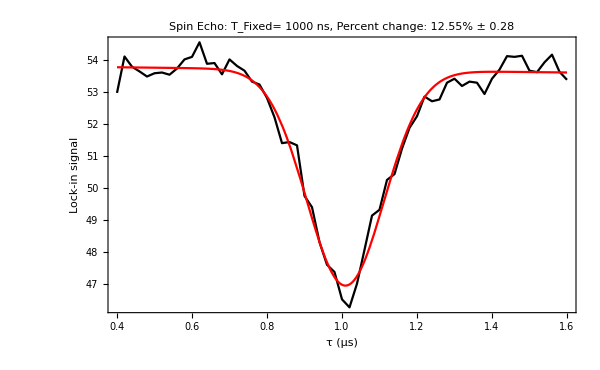

```mathematica
fileName="SiCe17 - 1 - Echo 1000ns.xls";
DropPointsBefore=0;
DropPointsAfter=0;
Include=False;

GaussianEcho[fileName,DropPointsBefore,DropPointsAfter,Include]
```

## Results

```mathematica
GraphTitle="Insert Graph Title: ";
LongTimeCutOff=5000;

EchoPlots[GraphTitle,LongTimeCutOff]
ActionMenu["Export Data",string//ToExpression]
```